# Prove of convergence for the contractive fixed point iteration

```mathematica
ClearAll["Global`*"]
```

### Define Matrix

```mathematica
SetDirectory[NotebookDirectory[]];
M=2;
Mp1=M+1;
size=(M+1)^2;
Nc=2*M+1;
ACCURACY=49;
ACCURACYPrint=20;
```

```mathematica
(*Gauss-Legendre nodes on reference interval[-1,1] ANALYTICAL*)Points=x/.Solve[LegendreP[M+1,x]==0,x];
Points=Sort[Re[Points],Less];
N[%]//MatrixForm
```

(-0.774597
0.
0.774597)

```mathematica
(*Derivative of Legendre Polynomial*)DLeg[x_]:=D[LegendreP[M+1,z],z]/.z->x;
```

```mathematica
Ws=Table[2/((1-(Points[[i]])^2)*(DLeg[Points[[i]]])^2),{i,1,M+1}];
N[%]//MatrixForm
```

(0.555556
0.888889
0.555556)

```mathematica
(*Gauss-Legendre nodes on reference interval[0,1] ANALYTICAL*)Points01=x/.Solve[LegendreP[M+1,x]==0,x];Points01=Re[(Points01+1)/2];
Points01=Sort[Points01,Less];
N[%]//MatrixForm
```

(0.112702
0.5
0.887298)

```mathematica
(* Lagrange Polynomials through Gauss-Legendre nodes *)

PSI[p_, ξ_] := ∏_(k=1)^(M+1) If[k!=p,(ξ-Points01[[k]])/(Points01[[p]]-Points01[[k]]),1]
```

```mathematica
(*Derivative of Lagrange Polynomials*)DPSI[p_,ξ_]:=D[PSI[p,x],x]/.x->ξ
```

```mathematica
(*Space-Time Polynomials*)θ[ξ_,τ_]:=Flatten[Table[Table[PSI[p,ξ]*PSI[q,τ],{p,1,M+1}],{q,1,M+1}]]
```

```mathematica
(*subindex definition*)
i1=Table[1+Mod[p-1,Mp1],{p,1,size}]
i2=Table[1+Quotient[q-Mod[q-1,Mp1],Mp1],{q,1,size}]
```

{1,2,3,1,2,3,1,2,3}

{1,1,1,2,2,2,3,3,3}

```mathematica
K1qp=Table[Table[If[i1[[p]]==i1[[q]],N[1/2 PSI[i2[[q]],1]*PSI[i2[[p]],1]*Ws[[i1[[p]]]]-1/4 Ws[[i1[[p]]]]*Ws[[i2[[p]]]]*DPSI[i2[[q]],Points01[[i2[[p]]]]],ACCURACY],0],{p,1,size}],{q,1,size}]//Simplify;
N[%]//MatrixForm
```

(0.308642 | 0. | 0. | 0.124598 | 0. | 0. | -0.0224533 | 0. | 0.
0. | 0.493827 | 0. | 0. | 0.199356 | 0. | 0. | -0.0359252 | 0.
0. | 0. | 0.308642 | 0. | 0. | 0.124598 | 0. | 0. | -0.0224533
-0.43324 | 0. | 0. | 0.123457 | 0. | 0. | 0.124598 | 0. | 0.
0. | -0.693183 | 0. | 0. | 0.197531 | 0. | 0. | 0.199356 | 0.
0. | 0. | -0.43324 | 0. | 0. | 0.123457 | 0. | 0. | 0.124598
0.176774 | 0. | 0. | -0.43324 | 0. | 0. | 0.308642 | 0. | 0.
0. | 0.282839 | 0. | 0. | -0.693183 | 0. | 0. | 0.493827 | 0.
0. | 0. | 0.176774 | 0. | 0. | -0.43324 | 0. | 0. | 0.308642)

```mathematica
Kxqp=Table[Table[If[i2[[p]]==i2[[q]],N[1/4 Ws[[i1[[q]]]]*Ws[[i2[[q]]]]*DPSI[i1[[p]],Points01[[i1[[q]]]]],ACCURACY],0],{p,1,size}],{q,1,size}]//Simplify;
N[%]//MatrixForm;
```

```mathematica
(*HERE MAYBE NUMERICAL INVERSE!?OTHERWISE VERY SLOW!*)K1qpInv=Inverse[K1qp]//Simplify;
N[%]//MatrixForm;
```

```mathematica
MatrixB=K1qpInv.Kxqp;
N[%]//MatrixForm
```

(-0.623981 | 0.831974 | -0.207994 | 0.31147 | -0.415293 | 0.103823 | -0.123981 | 0.165308 | -0.0413269
-0.207994 | 0. | 0.207994 | 0.103823 | 0. | -0.103823 | -0.0413269 | 0. | 0.0413269
0.207994 | -0.831974 | 0.623981 | -0.103823 | 0.415293 | -0.31147 | 0.0413269 | -0.165308 | 0.123981
-1.05533 | 1.40711 | -0.351777 | -1.07583 | 1.43444 | -0.35861 | 0.194669 | -0.259558 | 0.0648895
-0.351777 | 0. | 0.351777 | -0.35861 | 0. | 0.35861 | 0.0648895 | 0. | -0.0648895
0.351777 | -1.40711 | 1.05533 | 0.35861 | -1.43444 | 1.07583 | -0.0648895 | 0.259558 | -0.194669
-1.12398 | 1.49864 | -0.37466 | -1.68853 | 2.25137 | -0.562843 | -0.623981 | 0.831974 | -0.207994
-0.37466 | 0. | 0.37466 | -0.562843 | 0. | 0.562843 | -0.207994 | 0. | 0.207994
0.37466 | -1.49864 | 1.12398 | 0.562843 | -2.25137 | 1.68853 | 0.207994 | -0.831974 | 0.623981)

### Starting calculation for iteration scheme proof

```mathematica
Chop[N[Eigenvalues[MatrixB],16],10^-19]
```

{0,0,0,0,0,0,0,0,0}

```mathematica
(* dimension of kernel for different powers of matrix B *)
DimensionOfEigenspace =Table[size-MatrixRank[MatrixPower[MatrixB,p]],{p,1,size}]
```

{3,6,9,9,9,9,9,9,9}

```mathematica
(* geometrical multiplicity of EW = 0 (B^1)*)
DimensionOfEigenspace[[1]]
```

3

```mathematica
(* number of jordan blocks of size a+1!? *)
Table[2*DimensionOfEigenspace[[a]]-DimensionOfEigenspace[[a-1]]-DimensionOfEigenspace[[a+1]],{a,2,size-1}]
```

{0,3,0,0,0,0,0}

```mathematica
(* from this we know the structure of the Jordan blocks *)
Jblock = Table[Table[If[i==j+1,1,0],{i,1,Mp1}],{j,1,Mp1}];
N[%]//MatrixForm
JNull = Table[Table[0,{i,1,Mp1}],{j,1,Mp1}];
```

(0. | 1. | 0.
0. | 0. | 1.
0. | 0. | 0.)

```mathematica
(* construct full matrix J *)
MatrixJ = ArrayFlatten[Table[Table[If[i==j,Join[Jblock],Join[JNull]],{i,1,Mp1}],{j,1,Mp1}]];
N[%]//MatrixForm
```

(0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
(* from BP=PJ we see that we can choose Mp1 Eigenvectors independently *)
Pchosen=IdentityMatrix[size];
```

```mathematica
For[s=1,s≤ Mp1,s++,
For[p=1,p≤M,p++,Pchosen[[All,s*Mp1-p]]=MatrixB.(Pchosen[[All,s*Mp1-p+1]])]]
N[Pchosen,3]//MatrixForm
```

(0.0889 | -0.208 | 0 | -0.142 | 0.104 | 0 | 0.0957 | -0.0413 | 0
0.0889 | 0.208 | 0 | -0.142 | -0.104 | 0 | 0.0957 | 0.0413 | 0
0.0889 | 0.624 | 1. | -0.142 | -0.311 | 0 | 0.0957 | 0.124 | 0
0.7 | -0.352 | 0 | 0.222 | -0.359 | 0 | -0.0889 | 0.0649 | 0
0.7 | 0.352 | 0 | 0.222 | 0.359 | 0 | -0.0889 | -0.0649 | 0
0.7 | 1.06 | 0 | 0.222 | 1.08 | 1. | -0.0889 | -0.195 | 0
1.42 | -0.375 | 0 | 1.12 | -0.563 | 0 | 0.0889 | -0.208 | 0
1.42 | 0.375 | 0 | 1.12 | 0.563 | 0 | 0.0889 | 0.208 | 0
1.42 | 1.12 | 0 | 1.12 | 1.69 | 0 | 0.0889 | 0.624 | 1.)

```mathematica
PchosenInv = Inverse[Pchosen];
N[Chop[PchosenInv,10^-16],3]//MatrixForm
N[Chop[Pchosen.PchosenInv,10^-15],4]//MatrixForm
```

(0.725 | 0.725 | 0 | 0.728 | 0.728 | 0 | -0.0524 | -0.0524 | 0
-1.55 | 1.55 | 0 | -0.625 | 0.625 | 0 | 0.113 | -0.113 | 0
1. | -2. | 1. | 0 | 0 | 0 | 0 | 0 | 0
-1.14 | -1.14 | 0 | -0.775 | -0.775 | 0 | 0.455 | 0.455 | 0
1.36 | -1.36 | 0 | -0.387 | 0.387 | 0 | -0.391 | 0.391 | 0
0 | 0 | 0 | 1. | -2. | 1. | 0 | 0 | 0
2.85 | 2.85 | 0 | -1.83 | -1.83 | 0 | 0.725 | 0.725 | 0
-0.887 | 0.887 | 0 | 2.17 | -2.17 | 0 | -1.55 | 1.55 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | -2. | 1.)

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
(*Test...*)
test=(Pchosen.MatrixJ.PchosenInv);
MatrixB==test
```

True

```mathematica
(* Now we proved that this MatrixJ is the correct Jordan normal form of MatrixB *)
```

```mathematica
MatrixJPow = MatrixPower[MatrixJ,1];
```

```mathematica
(* check different powers of MatrixJ and see that it is the ZERO-matrix for a certain power (M+1) *)
For[s=0,MatrixJPow≠ConstantArray[0,{size,size}],s++,MatrixJPow=MatrixPower[MatrixJ,s+1]]
s
s==Mp1
```

3

True

# Comparison of Iteration scheme and RK in terms of function evaluations

```mathematica
(* approx Mp1 iterations (worst case) on Mp1^2 Gauss-Legendre nodes *)
fIter[x_] := (x+1)^3 + fCorr[x];
```

```mathematica
(* RK scheme with s stages *)
fRK[x_,s_] := (x+1)*s + fCorr[x];
```

```mathematica
(* compare assuming corrector takes Mp1^2 evaluations *)
s = {0,3,4,6,8,13,16};
fCorr[x_]:= (x+1)^2;
ADER= Table[{x,fIter[x]},{x,2,7}]
DGRK= Table[{x,fRK[x,s[[x]]]},{x,2,7}]
Quot = Table[{x,fIter[x]/fRK[x,s[[x]]]},{x,2,7}]
```

{{2,36},{3,80},{4,150},{5,252},{6,392},{7,576}}

{{2,18},{3,32},{4,55},{5,84},{6,140},{7,192}}

{{2,2},{3,5/2},{4,30/11},{5,3},{6,14/5},{7,3}}

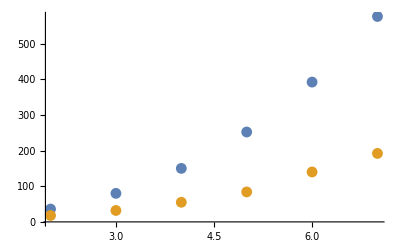

```mathematica
ListPlot[{ADER,DGRK}]
```

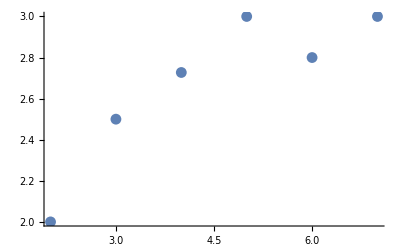

```mathematica
ListPlot[Quot]
```